## Process metadata

This process allows for some cleanup of the metadata gathered and re-exported into cleaner, easier to use EntityStores for exploration.

### Load Paclet

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
Get["CodeGolfSEAnalysis`"]
```

### Load prefetched EntityStores

These were generated in GatherMetadata.nb:

```mathematica
SetDirectory[NotebookDirectory[]];
codeGolfEntityStore=Import["codegolf.stackexchange.com_WithMetadata_2019-10-18_16-08-14.mx"];
EntityUnregister/@codeGolfEntityStore[];
EntityRegister[codeGolfEntityStore]

SetDirectory[NotebookDirectory[]];
codeGolfLanguageEntityStore=Import["CodeGolfProgrammingLanguage_2019-10-18_16-08-59.mx"];
EntityUnregister/@codeGolfLanguageEntityStore[];
EntityRegister[codeGolfLanguageEntityStore]
```

{StackExchange.Codegolf:User,StackExchange.Codegolf:Badge,StackExchange.Codegolf:Comment,StackExchange.Codegolf:Post,StackExchange:PostType,StackExchange.Codegolf:Vote,StackExchange:VoteType,StackExchange.Codegolf:PostHistory,StackExchange:PostHistoryType,StackExchange:CloseReason,StackExchange.Codegolf:Tag}

{CodeGolfProgrammingLanguage}

### Merge/Clean up programming language EntityStore

#### List of languages that can be merged

I manually sifted through the top several hundred and searched for possible duplicates.
Some of these are arbitrary, some are limitations to the name processing code.

```mathematica
languageToAlternatives=<|Entity["CodeGolfProgrammingLanguage","JavaScript::g3427"]->{Entity["CodeGolfProgrammingLanguage","javascriptes"],Entity["CodeGolfProgrammingLanguage","node.js"],Entity["CodeGolfProgrammingLanguage","nodejs"],Entity["CodeGolfProgrammingLanguage","node"],Entity["CodeGolfProgrammingLanguage","jses"],Entity["CodeGolfProgrammingLanguage","javascript/es"],Entity["CodeGolfProgrammingLanguage","js"]},
Entity["CodeGolfProgrammingLanguage","APL::nh588"]->{Entity["CodeGolfProgrammingLanguage","dyalogapl"],Entity["CodeGolfProgrammingLanguage","apl(dyalog"],Entity["CodeGolfProgrammingLanguage","dyalogaplextended"],Entity["CodeGolfProgrammingLanguage","apl(nars"],Entity["CodeGolfProgrammingLanguage","apl𝒿win"],Entity["CodeGolfProgrammingLanguage","aplnars"],Entity["CodeGolfProgrammingLanguage","apl𝒿score"],Entity["CodeGolfProgrammingLanguage","apl(dyalogclassic"],Entity["CodeGolfProgrammingLanguage","apl𝒿mauris"],Entity["CodeGolfProgrammingLanguage","apl𝒿size"]},
Entity["CodeGolfProgrammingLanguage","powershell"]->{Entity["CodeGolfProgrammingLanguage","WindowsPowerShell::886h5"],Entity["CodeGolfProgrammingLanguage","powershellcore"],Entity["CodeGolfProgrammingLanguage","powershell𝒿score"],Entity["CodeGolfProgrammingLanguage","powershell𝒿≤"],Entity["CodeGolfProgrammingLanguage","powershellforwindows"]},
Entity["CodeGolfProgrammingLanguage","WolframLanguage"]->{Entity["CodeGolfProgrammingLanguage","wolframmathematica"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿score"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿wolfram"],Entity["CodeGolfProgrammingLanguage","wolframmethematica"],Entity["CodeGolfProgrammingLanguage","wolfram≅"],Entity["CodeGolfProgrammingLanguage","mathematicasimplified"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿@martinender"],Entity["CodeGolfProgrammingLanguage","mathematicaonwindows"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿n="],Entity["CodeGolfProgrammingLanguage","mathematica𝒿size"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿l="]},
Entity["CodeGolfProgrammingLanguage","C::5zm8v"]->{Entity["CodeGolfProgrammingLanguage","csharp"],Entity["CodeGolfProgrammingLanguage","c𝒿sharp"],Entity["CodeGolfProgrammingLanguage","C::5zm8v"],Entity["CodeGolfProgrammingLanguage","c#.net"],Entity["CodeGolfProgrammingLanguage","c#inlinqpad"],Entity["CodeGolfProgrammingLanguage","c#𝒿linq"],Entity["CodeGolfProgrammingLanguage","c#𝒿linqpad"],Entity["CodeGolfProgrammingLanguage","c#wpf"],Entity["CodeGolfProgrammingLanguage","c#linq"]},
Entity["CodeGolfProgrammingLanguage","F::549k5"]->{Entity["CodeGolfProgrammingLanguage","fsharp"]},
Entity["CodeGolfProgrammingLanguage","><>"]->{Entity["CodeGolfProgrammingLanguage","><>fish"]},
Entity["CodeGolfProgrammingLanguage","C::p5vhv"]->{Entity["CodeGolfProgrammingLanguage","ANSIC::8zh69"],Entity["CodeGolfProgrammingLanguage","cpreprocessor"]},
Entity["CodeGolfProgrammingLanguage","PHP::x8873"]->{Entity["CodeGolfProgrammingLanguage","php>="]},
Entity["CodeGolfProgrammingLanguage","Brainfuck::8mj43"]->{Entity["CodeGolfProgrammingLanguage","brainf***"],Entity["CodeGolfProgrammingLanguage","brainf*ck"],Entity["CodeGolfProgrammingLanguage","self-modifyingbrainfu\[FreakedSmiley]\[FreakedSmiley]"],Entity["CodeGolfProgrammingLanguage","extendedbrainfu\[FreakedSmiley]\[FreakedSmiley]"],Entity["CodeGolfProgrammingLanguage","brainf**k"],Entity["CodeGolfProgrammingLanguage","bf"],Entity["CodeGolfProgrammingLanguage","smbf"],Entity["CodeGolfProgrammingLanguage","self-modifyingbrainf***"],Entity["CodeGolfProgrammingLanguage","self-modifyingbrainf*ck"],Entity["CodeGolfProgrammingLanguage","brainfu\[FreakedSmiley]\[FreakedSmiley]"],Entity["CodeGolfProgrammingLanguage","randombrainfu\[FreakedSmiley]\[FreakedSmiley]"]},
Entity["CodeGolfProgrammingLanguage","windowsbatch"]->{Entity["CodeGolfProgrammingLanguage","batchfile"],Entity["CodeGolfProgrammingLanguage","windowscommand"],Entity["CodeGolfProgrammingLanguage","windowsbatchfile"],Entity["CodeGolfProgrammingLanguage","windowscommandprompt"],Entity["CodeGolfProgrammingLanguage","batch"],Entity["CodeGolfProgrammingLanguage","cmd.exe"],Entity["CodeGolfProgrammingLanguage","windowscmd"],Entity["CodeGolfProgrammingLanguage","windowscommandshell"]},
Entity["CodeGolfProgrammingLanguage","Go::3m7v3"]->{Entity["CodeGolfProgrammingLanguage","golang"]},
Entity["CodeGolfProgrammingLanguage","Lua::9nnwp"]->{Entity["CodeGolfProgrammingLanguage","luaforwindows"]},
Entity["CodeGolfProgrammingLanguage","x86"]->{Entity["CodeGolfProgrammingLanguage","x86machine"],Entity["CodeGolfProgrammingLanguage","X86AssemblyLanguage::8wgc4"],Entity["CodeGolfProgrammingLanguage","x86_"],Entity["CodeGolfProgrammingLanguage","x86assembler"],Entity["CodeGolfProgrammingLanguage","x86"],Entity["CodeGolfProgrammingLanguage","x86opcode"],Entity["CodeGolfProgrammingLanguage","x8632-bitmachine"],Entity["CodeGolfProgrammingLanguage","x86machinecodeondos"],Entity["CodeGolfProgrammingLanguage","x86.com"],Entity["CodeGolfProgrammingLanguage","x86asm"],Entity["CodeGolfProgrammingLanguage","cpux86"],Entity["CodeGolfProgrammingLanguage","/32-bitx86assembly"],Entity["CodeGolfProgrammingLanguage","machinecodeonx86_"],Entity["CodeGolfProgrammingLanguage","x86andx"],Entity["CodeGolfProgrammingLanguage","x86opcode(.com"],Entity["CodeGolfProgrammingLanguage","x8616bitrealmodeassembly"],Entity["CodeGolfProgrammingLanguage","x86tasm"],Entity["CodeGolfProgrammingLanguage","x86machinecodeonms𝒿dos"],Entity["CodeGolfProgrammingLanguage","little𝒿endianx86machine"],Entity["CodeGolfProgrammingLanguage","x86ms𝒿dos.comfile"],Entity["CodeGolfProgrammingLanguage","x86machine𝒿code"]},
Entity["CodeGolfProgrammingLanguage","shakespeare"]->{Entity["CodeGolfProgrammingLanguage","shakespeareprogramming"]},
Entity["CodeGolfProgrammingLanguage","matlab/octave"]->{Entity["CodeGolfProgrammingLanguage","octave"],Entity["CodeGolfProgrammingLanguage","matlab𝒿octave"],Entity["CodeGolfProgrammingLanguage","matlab/octave"],Entity["CodeGolfProgrammingLanguage","octave𝒿matlab"],Entity["CodeGolfProgrammingLanguage","octave𝒿score"],Entity["CodeGolfProgrammingLanguage","MATLAB::82q2f"]},
Entity["CodeGolfProgrammingLanguage","Lisp::tnvy6"]->{Entity["CodeGolfProgrammingLanguage","CommonLisp::6p4h5"],Entity["CodeGolfProgrammingLanguage","EmacsLisp::5m82g"]}
|>;
languageToPreferredLanguage=languageToAlternatives//KeyValueMap[Thread[Rule[#2,#1]]&]//Flatten//DeleteDuplicates//Select[Apply[UnsameQ]]//Association;
```

```mathematica
languageToPreferredLanguage
```

<|JavaScript ES→JavaScript,Node.js→JavaScript,NodeJS→JavaScript,Node→JavaScript,JS ES→JavaScript,Javascript / ES→JavaScript,JS→JavaScript,Dyalog APL→APL,APL(Dyalog→APL,Dyalog APL Extended→APL,APL(NARS→APL,APL𝒥WIN→APL,APL NARS→APL,APL𝒥 score→APL,APL(Dyalog Classic→APL,APL𝒥 Mauris→APL,APL𝒥 size→APL,Windows PowerShell→PowerShell,PowerShell Core→PowerShell,PowerShell𝒥 score→PowerShell,Powershell𝒥 ≤→PowerShell,PowerShell for Windows→PowerShell,Wolfram Mathematica→Wolfram Language,Mathematica𝒥 score→Wolfram Language,Mathematica 𝒥 Wolfram→Wolfram Language,Wolfram Methematica→Wolfram Language,Wolfram ≅→Wolfram Language,Mathematica Simplified→Wolfram Language,Mathematica𝒥 @Martin Ender→Wolfram Language,Mathematica on Windows→Wolfram Language,Mathematica𝒥 n=→Wolfram Language,Mathematica𝒥 size→Wolfram Language,Mathematica𝒥 L=→Wolfram Language,CSharp→C#,C𝒥Sharp→C#,C# .NET→C#,C# in LINQPAD→C#,C# 𝒥 Linq→C#,C# 𝒥 LINQPad→C#,C# WPF→C#,C# LINQ→C#,FSharp→F#,><> Fish→><>,ANSI C→C,C Preprocessor→C,PHP>=→PHP,Brainf***→Brainfu\[FreakedSmiley]\[FreakedSmiley],Brainf*ck→Brainfu\[FreakedSmiley]\[FreakedSmiley],Self-modifying Brainfu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Extended BrainFu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Brainf**k→Brainfu\[FreakedSmiley]\[FreakedSmiley],BF→Brainfu\[FreakedSmiley]\[FreakedSmiley],SMBF→Brainfu\[FreakedSmiley]\[FreakedSmiley],Self-modifying Brainf***→Brainfu\[FreakedSmiley]\[FreakedSmiley],Self-modifying Brainf*ck→Brainfu\[FreakedSmiley]\[FreakedSmiley],Brainfu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Random Brainfu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Batch File→Windows batch,Windows Command→Windows batch,Windows Batch File→Windows batch,Windows Command Prompt→Windows batch,Batch→Windows batch,cmd.exe→Windows batch,Windows CMD→Windows batch,Windows command shell→Windows batch,Golang→Go,lua for windows→Lua,x86 Machine→x86,x86 assembly language→x86,x86_→x86,x86 Assembler→x86,x86 opcode→x86,x86 32-bit machine→x86,x86 machine code on DOS→x86,x86 .COM→x86,x86 asm→x86,CPU x86→x86,/32-bit x86 assembly→x86,MachineCode on x86_→x86,x86 and x→x86,x86 opcode(.COM→x86,x86 16 bit real mode Assembly→x86,x86 TASM→x86,x86 machine code on MS𝒥DOS→x86,little𝒥endian x86 machine→x86,x86 MS𝒥DOS .COM file→x86,x86 machine𝒥code→x86,Shakespeare Programming→Shakespeare,Octave→MATLAB/Octave,Matlab 𝒥 Octave→MATLAB/Octave,Octave 𝒥 MATLAB→MATLAB/Octave,Octave𝒥 score→MATLAB/Octave,MATLAB→MATLAB/Octave,Common Lisp→Lisp,Emacs Lisp→Lisp|>

#### Merge language entities in the Metadata

```mathematica
postToMetadata=EntityValue["StackExchange.Codegolf:Post","CodeGolfMetadata","EntityAssociation"];
postToMetadata//Length
```

154104

```mathematica
postToFixedMetadata=Replace[a_Association/;KeyMemberQ[a,"Language"]:>Append[a,"Language"->Lookup[languageToPreferredLanguage,a["Language"],a["Language"]]]]/@postToMetadata;
```

```mathematica
KeyValueMap[(#1["CodeGolfMetadata"]=.;#1["CodeGolfMetadata"]=#2;)&,postToFixedMetadata];//AbsoluteTiming
```

{52.8353,Null}

```mathematica
postToMetadata2=EntityValue["StackExchange.Codegolf:Post","CodeGolfMetadata","EntityAssociation"];
postToMetadata2//Length
```

154104

```mathematica
Select[postToMetadata2,#["Language"]===Entity["CodeGolfProgrammingLanguage","javascriptes"]&,1]
```

<||>

#### Merge and update language entities in the language EntityStore

```mathematica
languageToURLCounts=GroupBy[Select[Lookup[Values[postToMetadata2],{"Language","TitleURLs"}],FreeQ[_Missing]],First->Last,Flatten/*Counts/*ReverseSort]//ReverseSortBy[Total];
languageToURLCounts//Length
```

2472

```mathematica
Total/@languageToURLCounts[[;;12]]
```

<|Python→5115,Jelly→5026,05AB1E→3463,Perl→2601,APL→1885,MATL→1544,Haskell→1476,Japt→1426,Retina→1417,R→1182,C→1121,Ruby→1093|>

```mathematica
Keys/*First/@languageToURLCounts[[;;12]]
```

<|Python→https://docs.python.org/2/,Jelly→https://github.com/DennisMitchell/jelly,05AB1E→https://github.com/Adriandmen/05AB1E,Perl→https://www.perl.org/,APL→https://www.dyalog.com/,MATL→https://github.com/lmendo/MATL,Haskell→https://www.haskell.org/,Japt→https://github.com/ETHproductions/japt,Retina→https://github.com/m-ender/retina,R→https://www.r-project.org/,C→https://gcc.gnu.org/,Ruby→https://www.ruby-lang.org/|>

```mathematica
EntityValue["CodeGolfProgrammingLanguage","EntityCount"]
```

9637

```mathematica
ClearAll[mergeCodeGolfLanguages];
mergeCodeGolfLanguages[original_Entity,survivor_Entity]:=Module[
{},
If[MissingQ[EntityValue@Entity["ProgrammingLanguage",CanonicalName[survivor]]],
survivor["Labels"]=Join@@EntityValue[{original,survivor},"Labels"];
];
survivor["URLCounts"]=ReverseSortBy[Merge[Lookup[languageToURLCounts,{original,survivor},<||>],Total],Total];
original=.;
];
KeyValueMap[mergeCodeGolfLanguages,languageToPreferredLanguage];//AbsoluteTiming
```

{0.208002,Null}

```mathematica
EntityValue["CodeGolfProgrammingLanguage","EntityCount"]
```

9542

```mathematica
Entity["CodeGolfProgrammingLanguage", "JavaScript::g3427"]
```

JavaScript

### Add Additional Properties

#### Submission Programming Language

```mathematica
EntityProperty["StackExchange.Codegolf:Post","SubmissionProgrammingLanguage"]["Label"]="submission programming language";
EntityProperty["StackExchange.Codegolf:Post","SubmissionProgrammingLanguage"]["DefaultFunction"]=EntityFramework`BatchApplied[
Function[entities,Lookup[EntityValue[entities,"CodeGolfMetadata"],"Language",Missing["NotAvailable"]]]
];
Entity["StackExchange.Codegolf:Post","581"]["SubmissionProgrammingLanguage"]
```

GolfScript

#### Submission Reported Size

```mathematica
EntityProperty["StackExchange.Codegolf:Post","SubmissionReportedSize"]["Label"]="submission reported size";
EntityProperty["StackExchange.Codegolf:Post","SubmissionReportedSize"]["DefaultFunction"]=EntityFramework`BatchApplied[
Function[entities,Lookup[EntityValue[entities,"CodeGolfMetadata"],"ReportedSize",Missing["NotAvailable"]]]
];
Entity["StackExchange.Codegolf:Post","581"]["SubmissionReportedSize"]
```

26 characters

#### Submission Code Snippets

```mathematica
EntityProperty["StackExchange.Codegolf:Post","SubmissionCodeSnippets"]["Label"]="submission code snippets";
EntityProperty["StackExchange.Codegolf:Post","SubmissionCodeSnippets"]["DefaultFunction"]=EntityFramework`BatchApplied[
Function[entities,Lookup[EntityValue[entities,"CodeGolfMetadata"],"CodeSnippets",Missing["NotAvailable"]]]
];
Entity["StackExchange.Codegolf:Post","581"]["SubmissionCodeSnippets"]
```

{~:x,{:b;x,{b?x=b*}%+}*$-1>
}

#### Historical Code Golf Metadata

```mathematica
EntityProperty["StackExchange.Codegolf:Post","HistoricalCodeGolfMetadata"]=.;
EntityProperty["StackExchange.Codegolf:Post","HistoricalCodeGolfMetadata"]["Label"]="historical code golf metadata";
EntityProperty["StackExchange.Codegolf:Post","HistoricalCodeGolfMetadata"]["DefaultFunction"]=EntityFramework`BatchApplied[GetHistoricalCodeGolfMetadata,BatchSize->1000];
EntityValue[{Entity["StackExchange.Codegolf:Post","59017"],Entity["StackExchange.Codegolf:Post","603"],Entity["StackExchange.Codegolf:Post","5085"],Entity["StackExchange.Codegolf:Post","581"]},"HistoricalCodeGolfMetadata"]
```

{EventSeries[…],EventSeries[…],EventSeries[…],EventSeries[…]}

##### Example: Visualize Submission Size History for a thread

```mathematica
parentPost=Entity["StackExchange.Codegolf:Post","48937"];
submissions=EntityList@EntityClass["StackExchange.Codegolf:Post","ParentPost"->parentPost];
submissions//Length
```

13

```mathematica
submissionToHistoricalCodeGolfMetadata=EntityValue[submissions,"HistoricalCodeGolfMetadata","EntityAssociation"];//AbsoluteTiming
```

{74.5632,Null}

```mathematica
submissionToHistoricalCodeGolfMetadata[[;;3]]
```

<|A: [Logic Knight] Python 2, 300 bytes
This program uses join, lambda…[»](https://codegolf.stackexchange.com/q/48941)→EventSeries[…],A: [Martin Ender] CJam, 61 60 58 55 54 52 51 bytes
Shortened a bit…[»](https://codegolf.stackexchange.com/q/48943)→EventSeries[…],A: [Lars Ebert] PHP, 408, 407, 402, 387, 379 bytes
I am not a good…[»](https://codegolf.stackexchange.com/q/48946)→EventSeries[…]|>

```mathematica
TimeSeriesMap[Lookup["ReportedSize"],#]&/@submissionToHistoricalCodeGolfMetadata;
```

TODO: Make points have tooltips of code???

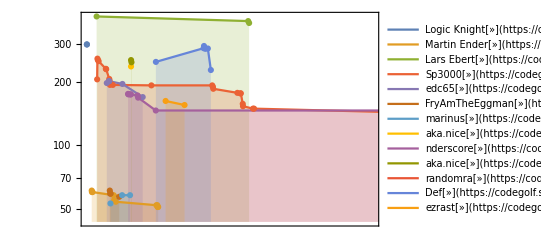

```mathematica
KeyValueMap[
Function[
{post,ts},
Legended[
Tooltip[{#1,QuantityMagnitude[#2["ReportedSize"]]},First[#2["CodeSnippets"],Missing["NotFound"]]]&@@@ts["Path"],
Row[post[{"Owner","SubmissionProgrammingLanguage","URL"}]/.url_URL:>Hyperlink[Style["»",18],url],Spacer[1]]
]
],
submissionToHistoricalCodeGolfMetadata
]//DateListLogPlot[#,Mesh->All,Filling->Axis]&
```

```mathematica
(* TODO: Explore if the rate fits this pretty well over lots of submissions? *)
Size[t_]:=size0+c1+Exp[-k*t]
```

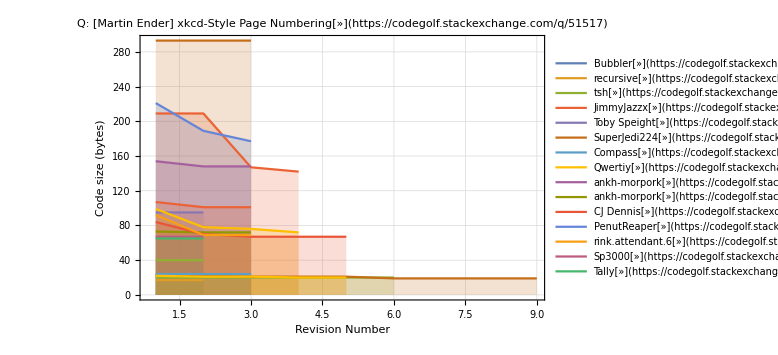

```mathematica
ListPlot[
(#["Values"]&/@DeleteMissing[submissionToSizeHistory])//KeyValueMap[Row[#1[{"Owner","SubmissionProgrammingLanguage","URL"}]/.url_URL:>Hyperlink[Style["»",18],url],Spacer[1]]->QuantityMagnitude[#2]&]//Association//KeySort//Reverse,
PlotRange->Full,
(*PlotLegends->None,*)
ImageSize->Large,
Filling->Axis,
Joined->True,
PlotTheme->"Detailed",
FrameLabel->{"Revision Number","Code size (bytes)"},
PlotLabel->Entity["StackExchange.Codegolf:Post","51517"]
]
```

#### Language URLCounts

```mathematica
EntityProperty["CodeGolfProgrammingLanguage","URLCounts"]["Label"]="URL counts";
EntityProperty["CodeGolfProgrammingLanguage","URLCounts"]["DefaultFunction"]=EntityFramework`BatchApplied[Lookup[languageToURLCounts,#,<||>]&/*Map[KeyMap[URL]]];
Entity["CodeGolfProgrammingLanguage","Rust::8y9w4"]["URLCounts"]
```

<|URL[https://www.rust-lang.org/]→58,URL[https://www.rust-lang.org/en-US/]→2,URL[http://www.rust-lang.org/]→2,URL[https://play.rust-lang.org/?version=stable&mode=debug&edition=2018&gist=309e94d8fe6a66c402a09901e9af5621]→1,URL[https://rust-lang.org]→1,URL[https://play.rust-lang.org/?version=stable&mode=debug&edition=2015&gist=3f493af80510e031bd0c7f85f4cd3497]→1,URL[https://oeis.org/A000141]→1,URL[https://oeis.org/A000001]→1,URL[http://rust-lang.org/]→1|>

#### Language URL

```mathematica
EntityProperty["CodeGolfProgrammingLanguage","URL"]["Label"]="URL";
EntityProperty["CodeGolfProgrammingLanguage","URL"]["DefaultFunction"]=EntityFramework`BatchApplied[
RightComposition[
EntityProperty["CodeGolfProgrammingLanguage","URLCounts"],
Keys,
Map[First[#,Missing["NotAvailable"]]&]
]
];
Entity["CodeGolfProgrammingLanguage","Rust::8y9w4"]["URL"]
```

URL[https://www.rust-lang.org/]

## Export cleaned up EntityStores

Export these cleaned up EntityStores for further exploration in Explore.nb:

```mathematica
SetDirectory[NotebookDirectory[]];
Export["codegolf.stackexchange.com_Cleaned_"<>StringReplace[DateString["ISODateTime"],{":"->"-","T"->"_"}]<>".mx",Entity["StackExchange.Codegolf:Post"]["EntityStore"]]
```

codegolf.stackexchange.com_Cleaned_2019-10-21_16-46-54.mx

```mathematica
SetDirectory[NotebookDirectory[]];
Export["CodeGolfProgrammingLanguage_Cleaned_"<>StringReplace[DateString["ISODateTime"],{":"->"-","T"->"_"}]<>".mx",Entity["CodeGolfProgrammingLanguage"]["EntityStore"]]
```

CodeGolfProgrammingLanguage_Cleaned_2019-10-21_16-47-34.mx